```mathematica
Quit
```

```mathematica
NotebookDirectory[]
```

/Users/esser/Documents/PROJECTS/ALPsPheno/ALP multibosons/notebooks/

## Invariant mass m_γγ for γγ

Take into account only the bins above 80 GeV, below there is no signal due to the p_Tcuts on the photons.

```mathematica
dataGaGa = {4.2810*10^-01,4.2035*10^-01,3.8503*10^-01,3.4085*10^-01,2.9805*10^-01,2.6119*10^-01,2.3047*10^-01,1.9566*10^-01,1.5638*10^-01,1.3549*10^-01,1.1357*10^-01,9.5813*10^-02,8.0987*10^-02,6.8060*10^-02,5.7413*10^-02,4.7718*10^-02,3.9756*10^-02,3.2742*10^-02,2.8390*10^-02,2.3032*10^-02,1.9383*10^-02,1.6359*10^-02,1.3345*10^-02,1.1714*10^-02,9.4913*10^-03,8.0543*10^-03,6.7986*10^-03,5.6124*10^-03,4.6797*10^-03,3.7002*10^-03,3.2789*10^-03,2.7735*10^-03,2.1960*10^-03,1.8226*10^-03,1.5456*10^-03,1.3746*10^-03,1.1750*10^-03,8.2160*10^-04,7.6731*10^-04,6.5148*10^-04,5.3129*10^-04,3.8804*10^-04,3.6501*10^-04,2.9556*10^-04,2.7553*10^-04,2.0955*10^-04,1.3774*10^-04,1.1936*10^-04,6.3375*10^-05,7.8519*10^-07};
```

```mathematica
dataUncGaGa = {4.7240*10^-03,4.2589*10^-03,4.0202*10^-03,3.5893*10^-03,2.3245*10^-03,2.8523*10^-03,2.2125*10^-03,1.8497*10^-03,1.5680*10^-03,1.4216*10^-03,1.1951*10^-03,1.2343*10^-03,8.5693*10^-04,9.3765*10^-04,7.7839*10^-04,5.8390*10^-04,6.4166*10^-04,5.6186*10^-04,4.9018*10^-04,5.0571*10^-04,3.6955*10^-04,3.9461*10^-04,3.7173*10^-04,2.7469*10^-04,2.8168*10^-04,2.4850*10^-04,1.9017*10^-04,1.5008*10^-04,1.6411*10^-04,1.2918*10^-04,1.3498*10^-04,1.0799*10^-04,8.9560*10^-05,7.7861*10^-05,8.0691*10^-05,6.4596*10^-05,6.2690*10^-05,5.3697*10^-05,5.2731*10^-05,4.4382*10^-05,3.8631*10^-05,3.8113*10^-05,2.7932*10^-05,3.1849*10^-05,1.6751*10^-05,1.5775*10^-05,1.0804*10^-05,6.3330*10^-06,4.9955*10^-06,6.4329*10^-08};
```

```mathematica
backgroundGaGa = {4.3771*10^-01,4.3397*10^-01,4.0713*10^-01,3.6729*10^-01,3.2250*10^-01,2.7890*10^-01,2.3908*10^-01,2.0201*10^-01,1.7067*10^-01,1.4340*10^-01,1.1954*10^-01,9.9349*10^-02,8.3245*10^-02,7.1280*10^-02,5.9191*10^-02,4.9340*10^-02,4.0925*10^-02,3.4344*10^-02,2.8365*10^-02,2.3557*10^-02,1.9626*10^-02,1.6266*10^-02,1.3604*10^-02,1.1297*10^-02,9.5297*10^-03,7.8720*10^-03,6.5990*10^-03,5.4891*10^-03,4.5219*10^-03,3.8017*10^-03,3.1528*10^-03,2.6685*10^-03,2.1883*10^-03,1.8048*10^-03,1.5260*10^-03,1.2865*10^-03,1.0259*10^-03,8.6850*10^-04,7.2488*10^-04,5.9818*10^-04,4.9894*10^-04,4.1692*10^-04,3.5470*10^-04,2.9278*10^-04,2.2567*10^-04,1.8890*10^-04,1.3962*10^-04,9.6392*10^-05,5.5331*10^-05,7.9661*10^-07};
```

```mathematica
signal0GaGa= {9.2981*10^-03,1.2046*10^-02,1.5116*10^-02,1.7084*10^-02,1.7061*10^-02,1.8639*10^-02,1.7558*10^-02,1.8029*10^-02,1.7849*10^-02,1.8792*10^-02,1.8129*10^-02,1.7731*10^-02,1.7406*10^-02,1.7060*10^-02,1.6395*10^-02,1.6244*10^-02,1.5244*10^-02,1.5246*10^-02,1.4320*10^-02,1.3694*10^-02,1.3161*10^-02,1.3029*10^-02,1.2525*10^-02,1.1759*10^-02,1.1114*10^-02,1.0719*10^-02,1.0268*10^-02,9.7014*10^-03,9.4194*10^-03,8.6397*10^-03,8.3301*10^-03,8.0971*10^-03,7.5640*10^-03,7.0297*10^-03,6.7045*10^-03,6.2707*10^-03,5.7600*10^-03,5.3190*10^-03,5.1515*10^-03,4.5938*10^-03,4.4183*10^-03,4.2664*10^-03,3.8499*10^-03,3.5057*10^-03,3.4782*10^-03,3.0326*10^-03,2.7301*10^-03,2.3514*10^-03,1.8770*10^-03,6.2236*10^-05};
```

```mathematica
binCenterGaGa={80,85,90,96,102,108,115,122,130,137,145,154,162,171,180,190,200,210,220,232,244,256,268,280,294,308,322,338,353,369,386,402,420,438,458,477,498,519,541,563,586,610,635,661,687,716,752,798,862,960,7010};
```

```mathematica
s2th = 0.22305;
```

```mathematica
NeventsGaGa[gg_, gp_]:=backgroundGaGa+signal0GaGa*(gg/4)^2*(gp/(4*s2th))^2;
```

```mathematica
chi2GaGa[gg_, gp_]:=Sum[((dataGaGa[[i]]-NeventsGaGa[gg,gp][[i]])/dataUncGaGa[[i]])^2,{i,0,Length[dataGaGa]}];
```

```mathematica
chi2minGaGa=FindMinimum[chi2GaGa[gg,gp],{{gg,0},{gp,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{513.602,{gg→0.,gp→0.}}

```mathematica
chi2binGaGa= Table[(((dataGaGa[[i]]-NeventsGaGa[gg,gp][[i]])/dataUncGaGa[[i]])^2-chi2minGaGa[[1]]/Length[dataGaGa])/(chi2GaGa[gg,gp]-chi2minGaGa[[1]]),{i,1,Length[dataGaGa]}];
```

```mathematica
Length[chi2binGaGa]
```

50

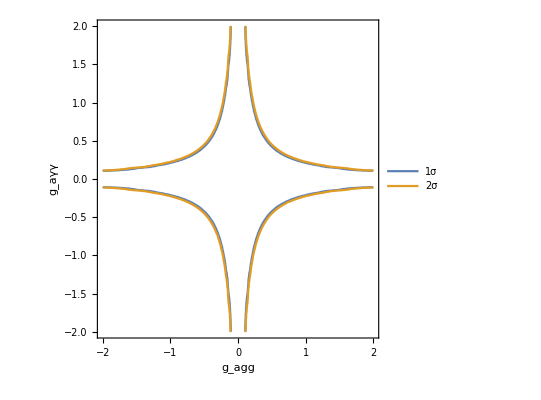

```mathematica
ContourPlot[{chi2GaGa[gg,gp]-chi2minGaGa[[1]]==1, chi2GaGa[gg,gp]-chi2minGaGa[[1]]==4},{gg,-2,2},{gp,-2,2} ,FrameLabel->(Style[#,14,Bold]&/@{Subscript[g, agg],Subscript[g, aγγ]}),PlotLegends->{"1σ", "2σ"}]
```

```mathematica
Reduce[chi2GaGa[gg,gp]-chi2minGaGa[[1]]==4, {gg,gp}][[2]][[4]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

gp==0.225847 √(1/gg^2)

```mathematica
FullSimplify[Reduce[chi2GaGa[gg,gp]-chi2minGaGa[[1]]==4, {gg,gp}][[2]][[4]], Assumptions->(gg>0)]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1. gg gp==0.225847

```mathematica
gpgg2sGaGa[gg_]:=0.225847/gg
```

```mathematica
1/gpgg2sGaGa[1]
```

4.42778

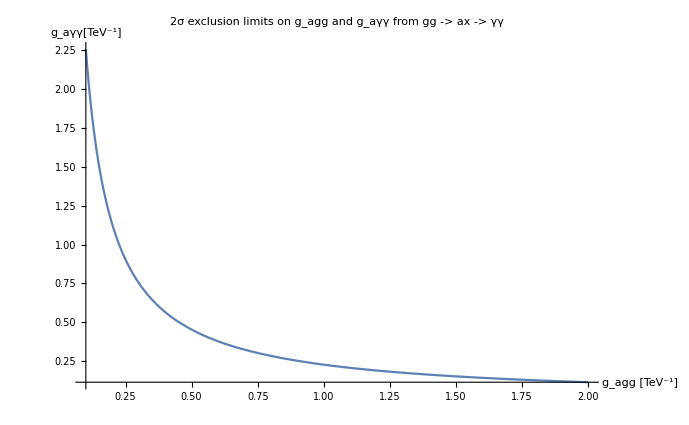

```mathematica
Plot[gpgg2sGaGa[gg], {gg,0.1,2}, PlotRange->Full, AxesLabel->{"g_agg [TeV^-1]","g_aγγ[TeV^-1]"}, PlotLabel->"2σ exclusion limits on g_agg and g_aγγ from gg -> ax -> γγ"]
```

χ^2 per bin for g_agg= 1 and g_aγγ= 0.22

```mathematica
chi2binGaGa/.{gg->1, gp->0.22}
```

{-2.33883,0.00922593,7.70446,16.9601,38.6861,10.9556,1.95728,0.677925,28.1947,8.14301,5.84829,-0.670361,-1.11751,0.766723,-1.79436,-0.749926,-2.53528,-0.591605,-3.935,-3.43744,-3.69546,-3.93173,-3.6757,-3.23238,-3.90498,-3.81202,-3.66315,-3.80928,-3.72458,-3.52199,-3.74877,-3.75532,-3.91522,-3.93136,-3.93435,-3.55702,-2.35843,-3.33776,-3.8644,-3.68645,-3.87421,-3.39995,-3.92722,-3.8944,-2.1027,-3.80814,-3.44334,-2.05499,-3.92364,1.75571}

Plot the χ^2 per bin minus the averaged χ^2per bin (i.e. χ^2/number of bins) and normalise by the total χ^2-(χ^2)_min:

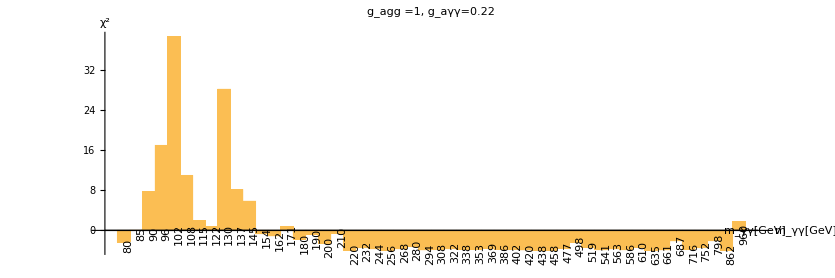

```mathematica
BarChart[chi2binGaGa/.{gg->1, gp->0.22},ChartLabels->Placed[binCenterGaGa,Below,Rotate[#,90 Degree]&], AxesLabel->{"m_γγ[GeV]", "χ^2"},PlotLabel->"g_agg =1, g_aγγ=0.22",AspectRatio->1/3]
```

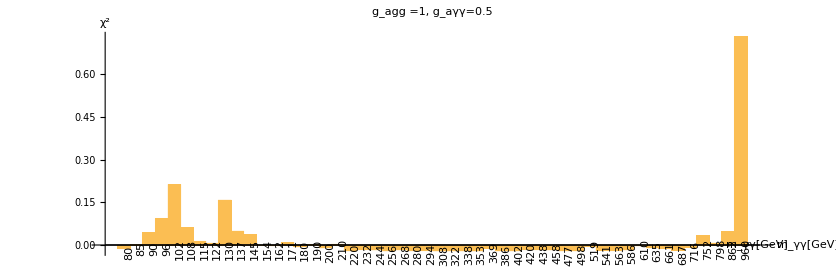

```mathematica
BarChart[chi2binGaGa/.{gg->1, gp->0.5},ChartLabels->Placed[binCenterGaGa,Below,Rotate[#,90 Degree]&], AxesLabel->{"m_γγ[GeV]", "χ^2"},PlotLabel->"g_agg =1, g_aγγ=0.5",AspectRatio->1/3]
```

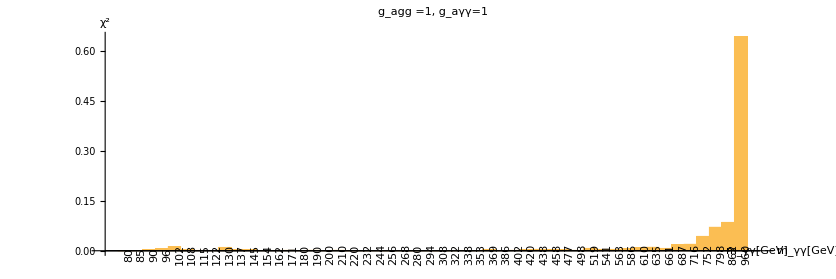

```mathematica
BarChart[chi2binGaGa/.{gg->1, gp->1},ChartLabels->Placed[binCenterGaGa,Below,Rotate[#,90 Degree]&], AxesLabel->{"m_γγ[GeV]", "χ^2"},PlotLabel->"g_agg =1, g_aγγ=1",AspectRatio->1/3]
```

## Invariant mass m_(4l) for ZZ

```mathematica
dataZZ = {2.6790*10^-01,3.6260*10^-01,2.3930*10^-01,2.3120*10^-01,1.4340*10^-01,9.0500*10^-02,5.7300*10^-02,3.3400*10^-02,2.8900*10^-02,2.0100*10^-02,4.6000*10^-03,1.2000*10^-03};
```

```mathematica
dataUncZZ = {3.5200*10^-02,3.9200*10^-02,3.1600*10^-02,2.7700*10^-02,2.1700*10^-02,1.5600*10^-02,1.2600*10^-02,8.4000*10^-03,6.9000*10^-03,4.5000*10^-03,1.9000*10^-03,3.0000*10^-04};
```

```mathematica
backgroundZZ ={2.9040*10^-01,3.4520*10^-01,2.6850*10^-01,1.9640*10^-01,1.3510*10^-01,9.3500*10^-02,6.4100*10^-02,4.3200*10^-02,2.7400*10^-02,1.5100*10^-02,6.8000*10^-03,1.2000*10^-03};
```

```mathematica
signal0ZZ={2.8596*10^-02,1.1408*10^-01,1.8962*10^-01,2.5545*10^-01,3.0437*10^-01,3.2787*10^-01,3.4578*10^-01,3.3858*10^-01,3.1820*10^-01,2.7929*10^-01,2.3138*10^-01,1.0795*10^-01};
```

```mathematica
binCenterZZ={190,210,230,252,278,305,335,370,415,480,570,910};
```

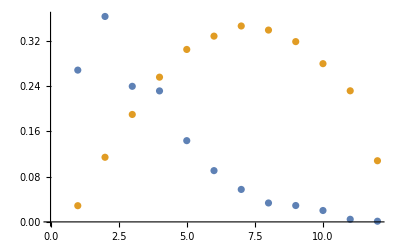

```mathematica
ListPlot[{dataZZ,signal0ZZ}]
```

```mathematica
s2th = 0.22305;
c2th = 1- s2th;
```

```mathematica
NeventsZZ[gg_, gZ_]:=backgroundZZ+signal0ZZ*(gg/4)^2*(gZ/(4*c2th))^2;
```

```mathematica
chi2ZZ[gg_, gZ_]:=Sum[((dataZZ[[i]]-NeventsZZ[gg,gZ][[i]])/dataUncZZ[[i]])^2,{i,0,Length[dataZZ]}];
```

```mathematica
chi2minZZ=FindMinimum[chi2ZZ[gg,gZ],{{gg,0},{gZ,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{7.49601,{gg→0.,gZ→0.}}

```mathematica
chi2binZZ= Table[(((dataZZ[[i]]-NeventsZZ[gg,gZ][[i]])/dataUncZZ[[i]])^2-chi2minZZ[[1]]/Length[dataZZ])/(chi2ZZ[gg,gZ]-chi2minZZ[[1]]),{i,1,Length[dataZZ]}];
```

```mathematica
Length[chi2binZZ]
```

12

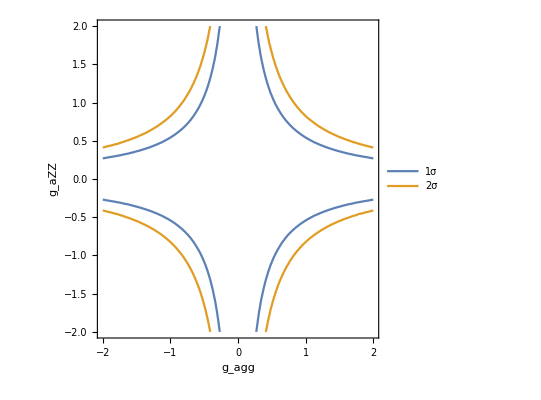

```mathematica
ContourPlot[{chi2ZZ[gg,gZ]-chi2minZZ[[1]]==1, chi2ZZ[gg,gZ]-chi2minZZ[[1]]==4},{gg,-2,2},{gZ,-2,2} ,FrameLabel->(Style[#,14,Bold]&/@{Subscript[g, agg],Subscript[g, aZZ]}),PlotLegends->{"1σ", "2σ"}]
```

```mathematica
Reduce[chi2ZZ[gg,gZ]-chi2minZZ[[1]]==4, {gg,gZ}][[2]][[4]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

gZ==0.825253 √(1/gg^2)

```mathematica
FullSimplify[Reduce[chi2ZZ[gg,gZ]-chi2minZZ[[1]]==4, {gg,gZ}][[2]][[4]], Assumptions->(gg>0)]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1. gg gZ==0.825253

```mathematica
gZgg2s[gg_]:=0.773998/gg
```

```mathematica
gZgg2s[1]
```

0.773998

```mathematica
1/gZgg2s[1]
```

1.29199

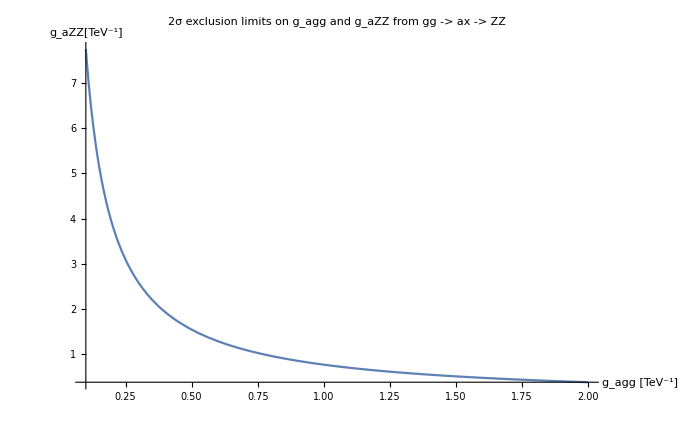

```mathematica
Plot[gZgg2s[gg], {gg,0.1,2}, PlotRange->Full, AxesLabel->{"g_agg [TeV^-1]","g_aZZ[TeV^-1]"}, PlotLabel->"2σ exclusion limits on g_agg and g_aZZ from gg -> ax -> ZZ"]
```

χ^2 per bin for g_agg= 1 and g_aZZ= 0.77

```mathematica
chi2binZZ/.{gg->1, gZ->0.77}
```

{-0.0674043,-0.139018,0.086533,0.275228,-0.164193,-0.174848,-0.0663199,0.356327,-0.198005,0.0436809,0.640814,0.407206}

Plot the χ^2 per bin minus the averaged χ^2per bin (i.e. χ^2/number of bins) and normalise by the total χ^2-(χ^2)_min:

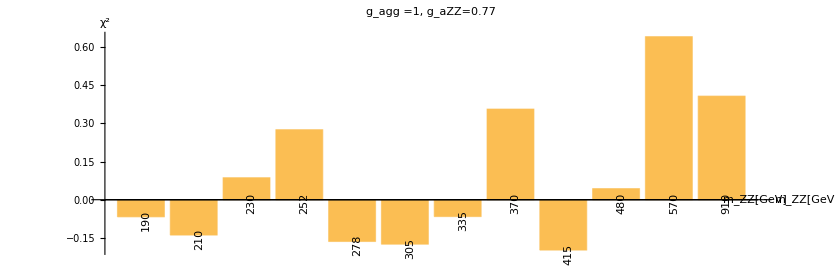

```mathematica
BarChart[chi2binZZ/.{gg->1, gZ->0.77},ChartLabels->Placed[binCenterZZ,Below,Rotate[#,90 Degree]&], AxesLabel->{"m_ZZ[GeV]", "χ^2"},PlotLabel->"g_agg =1, g_aZZ=0.77",AspectRatio->1/3]
```

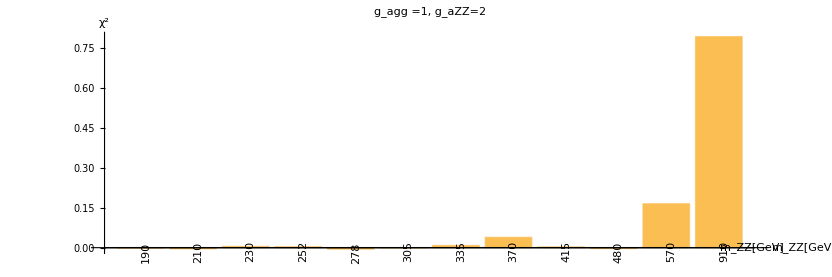

```mathematica
BarChart[chi2binZZ/.{gg->1, gZ->2},ChartLabels->Placed[binCenterZZ,Below,Rotate[#,90 Degree]&], AxesLabel->{"m_ZZ[GeV]", "χ^2"},PlotLabel->"g_agg =1, g_aZZ=2",AspectRatio->1/3]
```

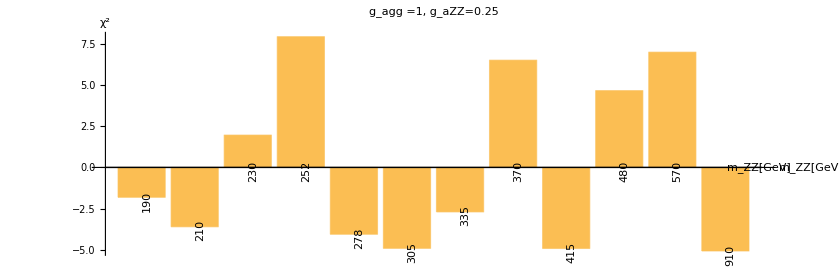

```mathematica
BarChart[chi2binZZ/.{gg->1, gZ->0.25},ChartLabels->Placed[binCenterZZ,Below,Rotate[#,90 Degree]&], AxesLabel->{"m_ZZ[GeV]", "χ^2"},PlotLabel->"g_agg =1, g_aZZ=0.25",AspectRatio->1/3]
```

The limits from ZZ are worse than the ones from γγ although the signal overshoots the data and background more in the former case. The reason is probably that the uncertainties for γγ are one order of magnitude smaller and there are more bins than for ZZ.

## pT of the leading jet for γZ

```mathematica
sigmaVBF[CB_,CW_]:=0.0010286470032311028 CB^4-0.0016001897983539096 CB^3 CW+0.009734562945808179 CB^2 CW^2-0.009354856465020562 CB CW^3+0.0058088939579702915 CW^4
```

```mathematica
dataGaZ ={1.9000*10^-02,1.3300*10^-02,5.6000*10^-03,1.0900*10^-03};
```

```mathematica
dataUncGaZ = {1.0000*10^-02,2.6000*10^-03,2.5000*10^-03,3.6000*10^-03};
```

```mathematica
backgroundGaZ ={1.7600*10^-02,1.4900*10^-02,5.2000*10^-03,5.9000*10^-04};
```

```mathematica
signal0GaZ={9.5962*10^-03,1.5910*10^-02,1.1561*10^-02,4.2197*10^-03};
```

```mathematica
binCenterGaZ={90,200,300,575};
```

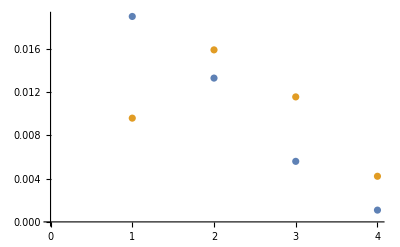

```mathematica
ListPlot[{dataGaZ,signal0GaZ}]
```

```mathematica
s2th = 0.22305;
c2th = 1- s2th;
```

```mathematica
NeventsGaZ[CB_, CW_]:=backgroundGaZ+signal0GaZ*sigmaVBF[CB,CW]/sigmaVBF[0,1];
```

```mathematica
chi2GaZ[CB_, CW_]:=Sum[((dataGaZ[[i]]-NeventsGaZ[CB,CW][[i]])/dataUncGaZ[[i]])^2,{i,0,Length[dataGaZ]}];
```

```mathematica
chi2minGaZ=FindMinimum[chi2GaZ[CB,CW],{{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.443188,{CB→0.,CW→0.}}

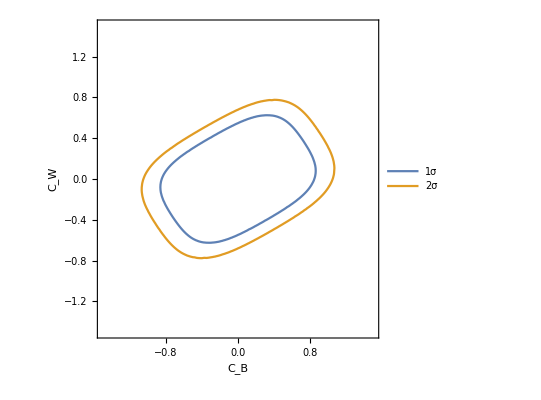

```mathematica
ContourPlot[{chi2GaZ[CB,CW]-chi2minGaZ[[1]]==1, chi2GaZ[CB,CW]-chi2minGaZ[[1]]==4},{CB,-1.5,1.5},{CW,-1.5,1.5} ,FrameLabel->(Style[#,14,Bold]&/@{Subscript[C, B],Subscript[C, W]}),PlotLegends->{"1σ", "2σ"}]
```

## Invariant mass m_eμ for WW

```mathematica
dataWW = {3.4530*10^+00,3.7670*10^+00,3.5380*10^+00,3.0940*10^+00,2.2280*10^+00,1.8990*10^+00,1.5580*10^+00,1.1450*10^+00,6.7460*10^-01,3.5160*10^-01,1.4070*10^-01,2.8370*10^-02,1.2700*10^-03};
```

```mathematica
dataUncWW = {1.0800*10^-01,1.3700*10^-01,1.3100*10^-01,1.0400*10^-01,8.8000*10^-02,8.1000*10^-02,6.3000*10^-02,4.9000*10^-02,3.3300*10^-02,1.8200*10^-02,9.1000*10^-03,2.8600*10^-03,2.7000*10^-04};
```

```mathematica
backgroundWW = {2.8916*10^+00,3.3367*10^+00,3.1062*10^+00,2.6919*10^+00,2.2508*10^+00,1.8158*10^+00,1.3637*10^+00,1.0615*10^+00,6.4312*10^-01,3.3767*10^-01,1.2847*10^-01,2.5664*10^-02,1.2695*10^-03};
```

```mathematica
signal0WW= {7.7175*10^+00,8.2990*10^+00,8.8564*10^+00,9.2790*10^+00,9.1112*10^+00,8.8554*10^+00,8.4953*10^+00,8.2097*10^+00,7.1297*10^+00,5.7175*10^+00,3.8732*10^+00,1.8837*10^+00,3.0883*10^-01};
```

```mathematica
binCenterWW={65,80,90,102,118,132,150,172,202,250,330,490,1050};
```

```mathematica
s2th = 0.22305;
```

```mathematica
NeventsWW[gg_, gW_]:=backgroundWW+signal0WW*(gg/4)^2*(gW/4)^2;
```

```mathematica
chi2WW[gg_, gW_]:=Sum[((dataWW[[i]]-NeventsWW[gg,gW][[i]])/dataUncWW[[i]])^2,{i,0,Length[dataWW]}];
```

```mathematica
chi2minWW=FindMinimum[chi2WW[gg,gW],{{gg,0},{gW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{80.4181,{gg→0.,gW→0.}}

```mathematica
chi2binWW= Table[(((dataWW[[i]]-NeventsWW[gg,gW][[i]])/dataUncWW[[i]])^2-chi2minWW[[1]]/Length[dataWW])/(chi2WW[gg,gW]-chi2minWW[[1]]),{i,1,Length[dataWW]}];
```

```mathematica
Length[chi2binWW]
```

13

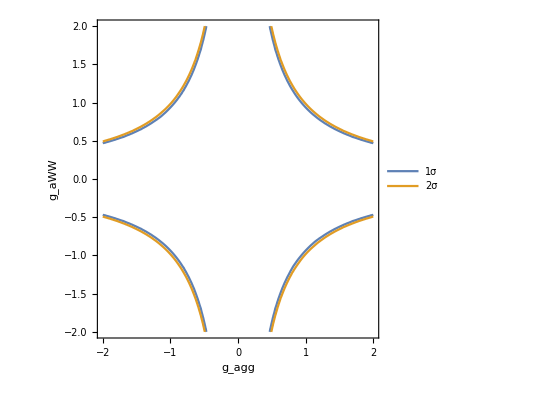

```mathematica
ContourPlot[{chi2WW[gg,gW]-chi2minWW[[1]]==1,chi2WW[gg,gW]-chi2minWW[[1]]==4},{gg,-2,2},{gW,-2,2} ,FrameLabel->(Style[#,14,Bold]&/@{Subscript[g, agg],Subscript[g, aWW]}),PlotLegends->{"1σ", "2σ"}]
```

```mathematica
Reduce[chi2WW[gg,gW]-chi2minWW[[1]]==4, {gg,gW}][[2]][[4]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

gW==0.984449 √(1/gg^2)

```mathematica
FullSimplify[Reduce[chi2WW[gg,gW]-chi2minWW[[1]]==4, {gg,gW}][[2]][[4]], Assumptions->(gg>0)]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1. gg gW==0.984449

```mathematica
gWgg2sWW[gg_]:=0.9844492500351121/gg
```

```mathematica
1/gWgg2sWW[1]
```

1.0158

χ^2 per bin for g_agg= 1 and g_aWW= 0.98

```mathematica
chi2binWW/.{gg->1, gW->0.98}
```

{4.91376,0.624585,0.832845,1.70478,-1.56386,-1.57431,0.125106,-1.36386,-1.67208,-1.63126,-1.66022,-1.04708,3.3116}

Plot the χ^2 per bin minus the averaged χ^2per bin (i.e. χ^2/number of bins) and normalise by the total χ^2-(χ^2)_min:

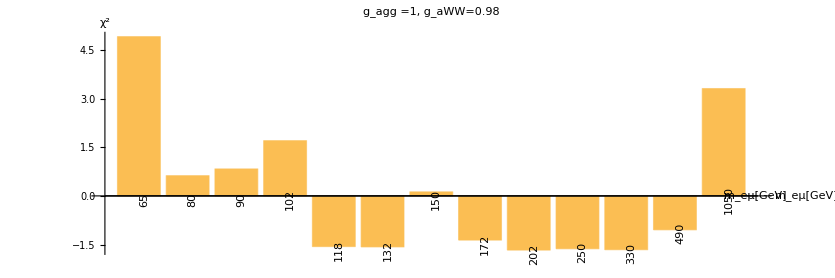

```mathematica
BarChart[chi2binWW/.{gg->1, gW->0.98},ChartLabels->Placed[binCenterWW,Below,Rotate[#,90 Degree]&], AxesLabel->{"m_eμ[GeV]", "χ^2"},PlotLabel->"g_agg =1, g_aWW=0.98",AspectRatio->1/3]
```

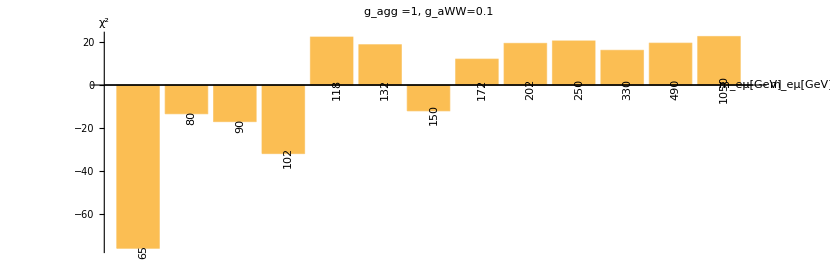

```mathematica
BarChart[chi2binWW/.{gg->1, gW->0.1},ChartLabels->Placed[binCenterWW,Below,Rotate[#,90 Degree]&], AxesLabel->{"m_eμ[GeV]", "χ^2"},PlotLabel->"g_agg =1, g_aWW=0.1",AspectRatio->1/3]
```

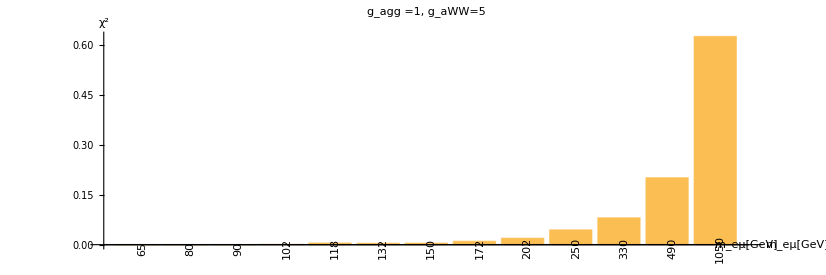

```mathematica
BarChart[chi2binWW/.{gg->1, gW->5},ChartLabels->Placed[binCenterWW,Below,Rotate[#,90 Degree]&], AxesLabel->{"m_eμ[GeV]", "χ^2"},PlotLabel->"g_agg =1, g_aWW=5",AspectRatio->1/3]
```

## Combined χ^2

```mathematica
(* fix fa = 1 TeV *)
fa=1;
```

```mathematica
gP[CB_,CW_]:= 4/fa*(c2th*CB+s2th*CW)
```

```mathematica
gZ[CB_,CW_]:=4/fa*(s2th*CB+c2th*CW)
```

```mathematica
gW[CW_]:= 4/fa CW
```

```mathematica
gg[CG_]:=4/fa CG
```

### Combine χ^2 for γγ and ZZ

#### 2D plot for CB and CW

Combined χ^2 for γγ and ZZ, fix CG=1

```mathematica
chi2tot2D[CB_,CW_]:= chi2GaGa[gg[1], gP[CB,CW]]-chi2minGaGa[[1]]+chi2ZZ[gg[1], gZ[CB,CW]]-chi2minZZ[[1]]
```

```mathematica
chi2mintot2D=FindMinimum[chi2tot2D[CB,CW],{{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{-1.13687×10^-13,{CB→0.,CW→0.}}

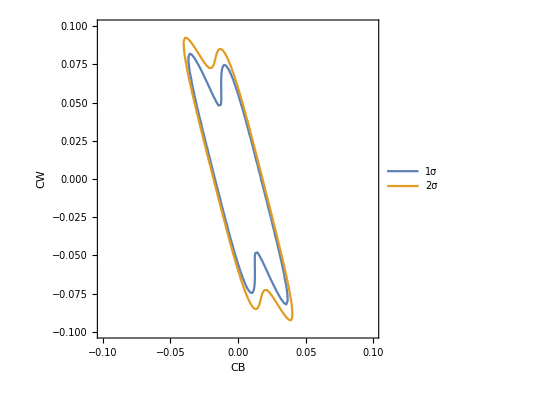

```mathematica
P2D=ContourPlot[{chi2tot2D[CB,CW]-chi2mintot2D[[1]]==1, chi2tot2D[CB,CW]-chi2mintot2D[[1]]==4},{CB,-0.1,0.1},{CW,-0.1,0.1} ,Axes->True,AxesLabel->{"CB", "CW"},PlotLegends->{"1σ", "2σ"}]
```

#### 3D plot for CG, CB and CW

```mathematica
chi2tot3D[CG_,CB_,CW_]:= chi2GaGa[gg[CG], gP[CB,CW]]-chi2minGaGa[[1]]+chi2ZZ[gg[1], gZ[CB,CW]]-chi2minZZ[[1]]
```

```mathematica
chi2mintot3D=FindMinimum[chi2tot3D[CG,CB,CW],{{CG,0},{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{-1.13687×10^-13,{CG→0.,CB→0.,CW→0.}}

```mathematica
P3D=ContourPlot3D[{chi2tot3D[CG,CB,CW]-chi2mintot3D[[1]]==2.3, chi2tot[CG,CB,CW]-chi2mintot3D[[1]]==6.2},{CG,-0.2,0.2},{CB,-0.2,0.2},{CW,-0.2,0.2} ,Axes->True,AxesLabel->{"CG", "CB", "CW"},PlotLegends->{"1σ", "2σ"}]
```

-Graphics3D-

### Combine χ^2 for γγ, ZZ and γZ

#### 2D plot for CB and CW

Combined χ^2 for γγ and ZZ and γZ, fix CG=1

```mathematica
chi2tot2D[CB_,CW_]:= chi2GaGa[gg[1], gP[CB,CW]]-chi2minGaGa[[1]]+chi2ZZ[gg[1], gZ[CB,CW]]-chi2minZZ[[1]] +chi2GaZ[CB,CW]-chi2minGaZ[[1]]
```

```mathematica
chi2mintot2D=FindMinimum[chi2tot2D[CB,CW],{{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{1.13687×10^-13,{CB→0.,CW→0.}}

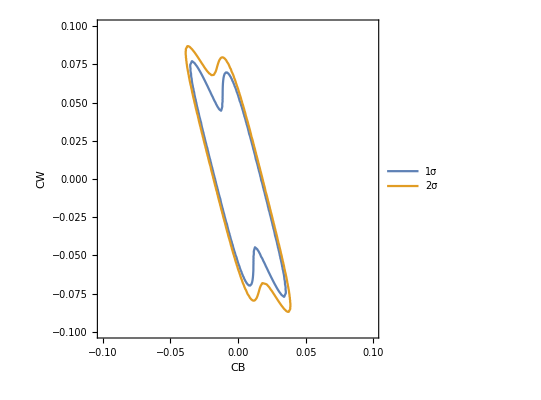

```mathematica
P2D=ContourPlot[{chi2tot2D[CB,CW]-chi2mintot2D[[1]]==1, chi2tot2D[CB,CW]-chi2mintot2D[[1]]==4},{CB,-0.1,0.1},{CW,-0.1,0.1} ,Axes->True,AxesLabel->{"CB", "CW"},PlotLegends->{"1σ", "2σ"}]
```

It looks like adding γZ does not change the limits much. Without γZ the individual limits for CB and CW are already of the order 0.02 and 0.06, respectively, and thus more than one order of magnitude better than the limits from γZ.

#### 3D plot for CG, CB and CW

```mathematica
chi2tot[CG_,CB_,CW_]:= chi2GaGa[gg[CG], gP[CB,CW]]-chi2minGaGa[[1]]+chi2ZZ[gg[1], gZ[CB,CW]]-chi2minZZ[[1]]+chi2GaZ[CB,CW]-chi2minGaZ[[1]]
```

```mathematica
chi2mintot=FindMinimum[chi2tot[CG,CB,CW],{{CG,0},{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{1.13687×10^-13,{CG→0.,CB→0.,CW→0.}}

```mathematica
P1=ContourPlot3D[{chi2tot[CG,CB,CW]-chi2mintot[[1]]==2.3, chi2tot[CG,CB,CW]-chi2mintot[[1]]==6.2},{CG,-0.2,0.2},{CB,-0.2,0.2},{CW,-0.2,0.2} ,AxesLabel->{"CG", "CB", "CW"},PlotLegends->{"1σ", "2σ"}]
```

-Graphics3D-

### Combine χ^2 for γγ, ZZ, γZ and WW

#### 2D plot for CB and CW

Combined χ^2 for γγ and ZZ and γZ, fix CG=1

```mathematica
chi2tot2D[CB_,CW_]:= chi2GaGa[gg[1], gP[CB,CW]]-chi2minGaGa[[1]]+chi2ZZ[gg[1], gZ[CB,CW]]-chi2minZZ[[1]] +chi2GaZ[CB,CW]-chi2minGaZ[[1]]+chi2WW[gg[1], gW[CW]]- chi2minWW[[1]]
```

```mathematica
chi2mintot2D=FindMinimum[chi2tot2D[CB,CW],{{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{1.13687×10^-13,{CB→0.,CW→0.}}

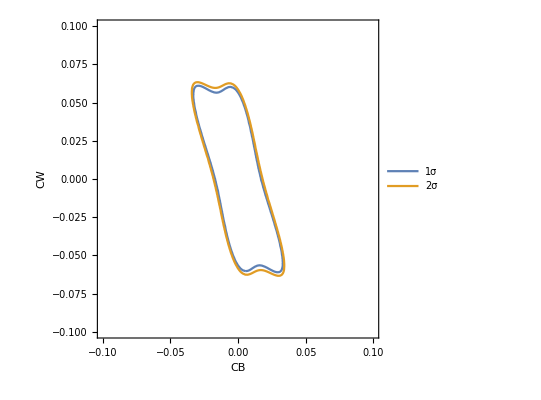

```mathematica
P2D=ContourPlot[{chi2tot2D[CB,CW]-chi2mintot2D[[1]]==1, chi2tot2D[CB,CW]-chi2mintot2D[[1]]==4},{CB,-0.1,0.1},{CW,-0.1,0.1} ,Axes->True,AxesLabel->{"CB", "CW"},PlotLegends->{"1σ", "2σ"}]
```

WW constrains only CW, a bit better than without WW.

#### 3D plot for CG, CB and CW

```mathematica
chi2tot[CG_,CB_,CW_]:= chi2GaGa[gg[CG], gP[CB,CW]]-chi2minGaGa[[1]]+chi2ZZ[gg[1], gZ[CB,CW]]-chi2minZZ[[1]]+chi2GaZ[CB,CW]-chi2minGaZ[[1]]+chi2WW[gg[CG], gW[CW]]- chi2minWW[[1]]
```

```mathematica
chi2mintot=FindMinimum[chi2tot[CG,CB,CW],{{CG,0},{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{1.13687×10^-13,{CG→0.,CB→0.,CW→0.}}

```mathematica
P1=ContourPlot3D[{chi2tot[CG,CB,CW]-chi2mintot[[1]]==2.3, chi2tot[CG,CB,CW]-chi2mintot[[1]]==6.2},{CG,-0.2,0.2},{CB,-0.2,0.2},{CW,-0.2,0.2} ,AxesLabel->{"CG", "CB", "CW"},PlotLegends->{"1σ", "2σ"}]
```

-Graphics3D-